FittedModel[1.70429-0.173891 x+0.00921391 x^2]

FittedModel[-13.4072+10.3233 ⅇ^(0.0217741 x)]

FittedModel[-13.4072+10.3233 1.02201^x]

NonlinearModelFit::nrlnum: The function value {204.146+123.362 ⅈ,245.648+123.362 ⅈ,250.675+123.362 ⅈ,248.888+123.362 ⅈ,«19»+«1»,238.339+123.362 ⅈ,231.509+123.362 ⅈ,224.025+123.362 ⅈ,216.19+123.362 ⅈ} is not a list of real numbers with dimensions {9} at {a,b,c,d} = {39.2674,-72.736,176.263,-52.4921}.

FittedModel[-52.4921+39.2674 Log[176.263-72.736 x]]

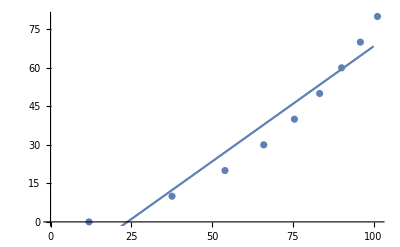

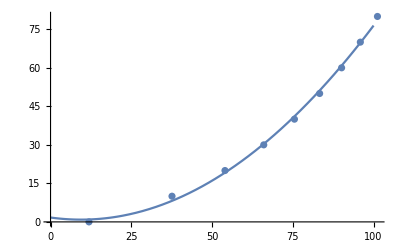

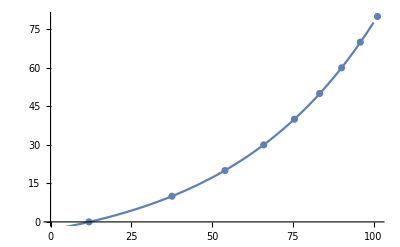

-Graphics-

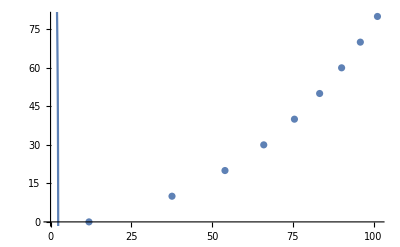

```mathematica
T={0,10,20,30,40,50,60,70,80};
V={11.9,37.6,54,66,75.5,83.3,90.1,95.9,101.2};
data = Thread[{V,T}];
lm=LinearModelFit[data,x,x];
nlm1=NonlinearModelFit[data,a x^2+b x+c,{a,b,c},x,MaxIterations->1000000]
nlm2=NonlinearModelFit[data,a ⅇ^(b x)+c,{a,{b,0.5},c},x,MaxIterations->1000000]
nlm3=NonlinearModelFit[data,a b^x+c,{a,b,c},x,MaxIterations->10000]
nlm4=NonlinearModelFit[data,a Log[b x + c]+d,{a,b,c,{d,18}},x,MaxIterations->1000000]
Show[ListPlot[data],Plot[lm[x],{x,0,100}]]
Show[ListPlot[data],Plot[nlm1[x],{x,0,100}]]
Show[ListPlot[data],Plot[nlm2[x],{x,0,100}]]
Show[ListPlot[data],Plot[nlm3[x],{x,0,100}]]
Show[ListPlot[data],Plot[nlm4[x],{x,0,100}]]
```

```mathematica
Quit
```